```mathematica
ClearAll["Global`*"]
R1=48;

res=out/.NDSolve[{out'[t]==t*R1, out[0]==1},out, {t,0,10}, Method->"ExplicitRungeKutta",MaxStepSize->0.1][[1]];
resNumber=res[2]
```

97.

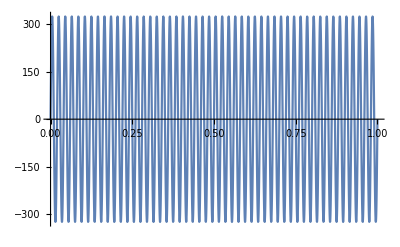

```mathematica
Plot[Sqrt[2]*230*Sin[2*Pi*50*t],{t,0,1}]
```

```mathematica
fce[t_]:=Sqrt[2]*230*Sin[2*Pi*50*t];
fce[5*10^(-3)]
```

230 √2

```mathematica
N[5*10^(-3)]
```

0.005

```mathematica
N[Pi*120/180]
```

2.0944

```mathematica
R1=0.370;
R2=0.225;
L1s=0.00227;
L2s=0.00227;
Lm=0.0825;
L1=0.08477;
L2=0.08477;
pp=2;
intertia=0.4;
sigma=1-Lm^2/(L1*L2);
sigma
```

0.0528396

# MODEL GRAPHICAL TESTING

```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];

ctuBlue=RGBColor["#0065BD"];
ctuLightBlue=RGBColor["#6AADE4"];
ctuRed=RGBColor["#C60C30"];
ctuGreen=RGBColor["#A2AD00"];
ctuGreenyBlue=RGBColor["#00B2A9"];
ctuOrange=RGBColor["#E05206"];
ctuYellow=RGBColor["#F0AB00"];
```

## ASM model selected outputs

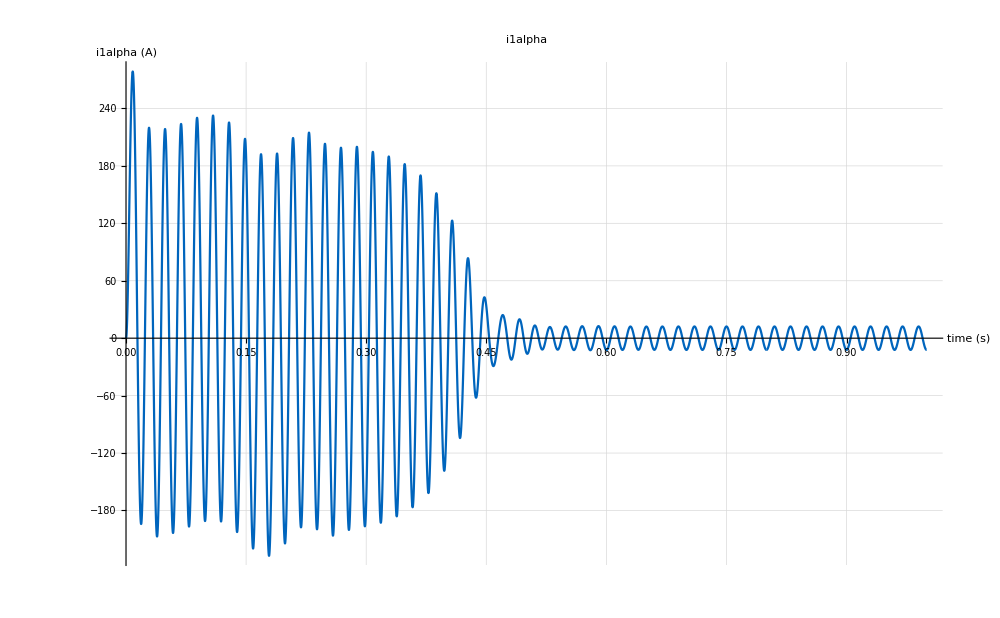

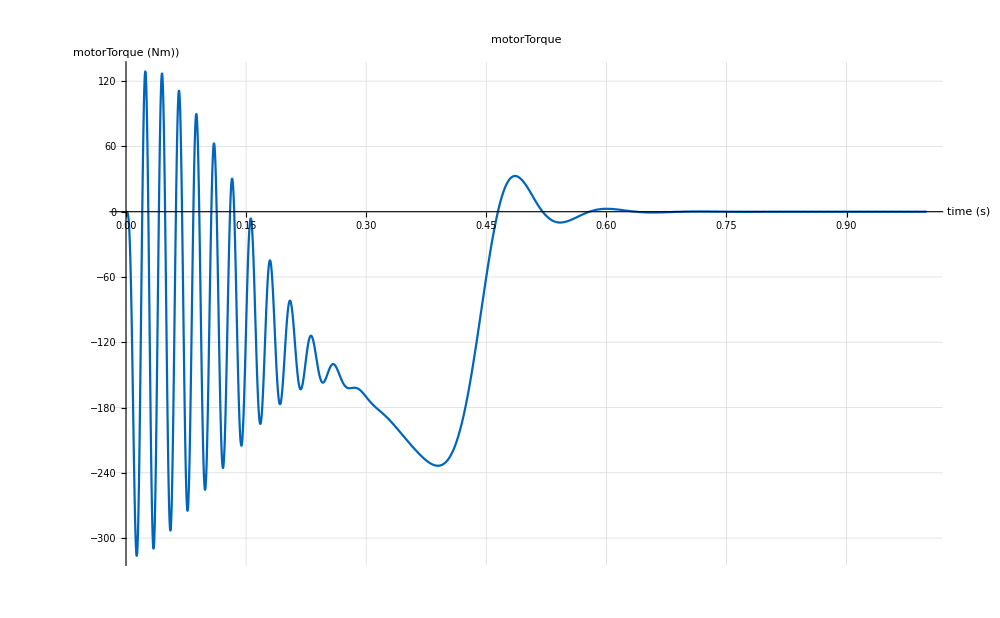

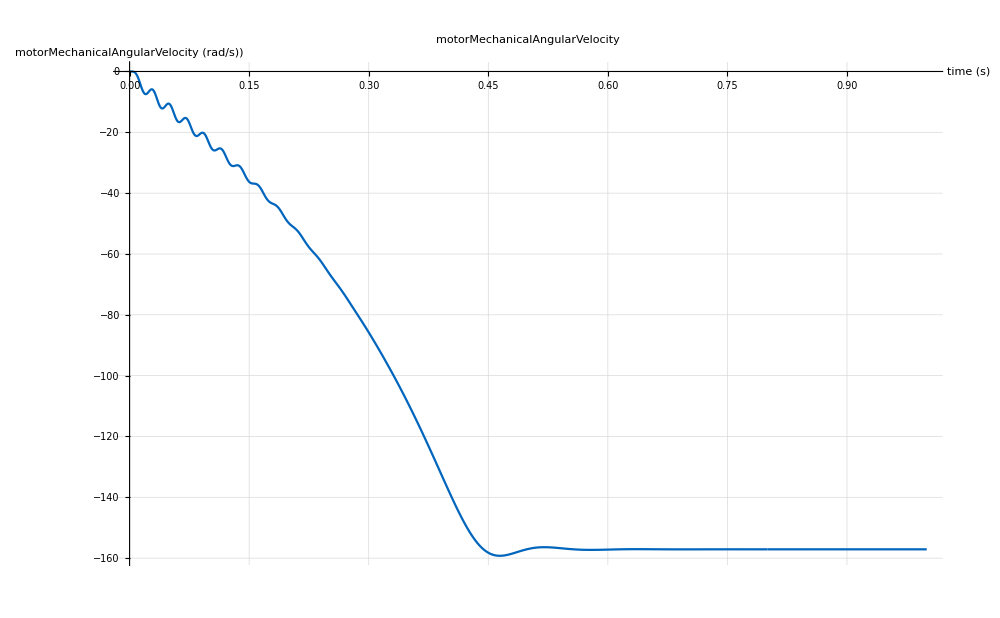

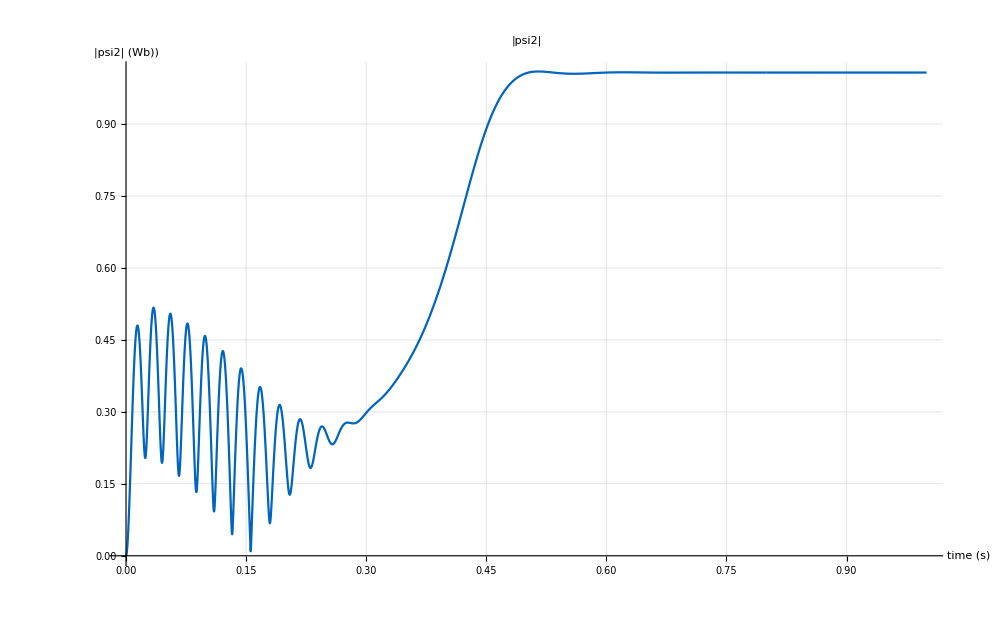

```mathematica
data=Import["./../code/cmodel/outputASM.csv"];
ListPlot[data[[All,1;;2]],Joined->True,PlotStyle->ctuBlue,LabelStyle->{FontFamily->"Times New Roman",15,Black, Bold},AxesOrigin->{0,0},GridLines->Automatic,AxesLabel->{"time (s)","i1alpha (A)"},PlotLabel->"i1alpha",PlotRangeClipping->False,ImageSize->1000,PlotRange->All]

ListPlot[data[[All,{1,3}]],Joined->True,PlotStyle->ctuBlue,LabelStyle->{FontFamily->"Times New Roman",15,Black, Bold},AxesOrigin->{0,0},GridLines->Automatic,AxesLabel->{"time (s)","u1alpha (V)"},PlotLabel->"u1alpha",PlotRangeClipping->False,ImageSize->1000,PlotRange->All];

ListPlot[data[[All,{1,4}]],Joined->True,PlotStyle->ctuBlue,LabelStyle->{FontFamily->"Times New Roman",15,Black, Bold},AxesOrigin->{0,0},GridLines->Automatic,AxesLabel->{"time (s)","motorTorque (Nm))"},PlotLabel->"motorTorque",PlotRangeClipping->False,ImageSize->1000,PlotRange->All]

ListPlot[data[[All,{1,5}]],Joined->True,PlotStyle->ctuBlue,LabelStyle->{FontFamily->"Times New Roman",15,Black, Bold},AxesOrigin->{0,0},GridLines->Automatic,AxesLabel->{"time (s)","motorMechanicalAngularVelocity (rad/s))"},PlotLabel->"motorMechanicalAngularVelocity",PlotRangeClipping->False,ImageSize->1000,PlotRange->All]

ListPlot[data[[All,{1,6}]],Joined->True,PlotStyle->ctuBlue,LabelStyle->{FontFamily->"Times New Roman",15,Black, Bold},AxesOrigin->{0,0},GridLines->Automatic,AxesLabel->{"time (s)","|psi2| (Wb))"},PlotLabel->"|psi2|",PlotRangeClipping->False,ImageSize->1000,PlotRange->All]
```

## ASM current – velocity (I-n) model directly from ASM model values vs values from inverse clark

```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];

ctuBlue=RGBColor["#0065BD"];
ctuLightBlue=RGBColor["#6AADE4"];
ctuRed=RGBColor["#C60C30"];
ctuGreen=RGBColor["#A2AD00"];
ctuGreenyBlue=RGBColor["#00B2A9"];
ctuOrange=RGBColor["#E05206"];
ctuYellow=RGBColor["#F0AB00"];
```

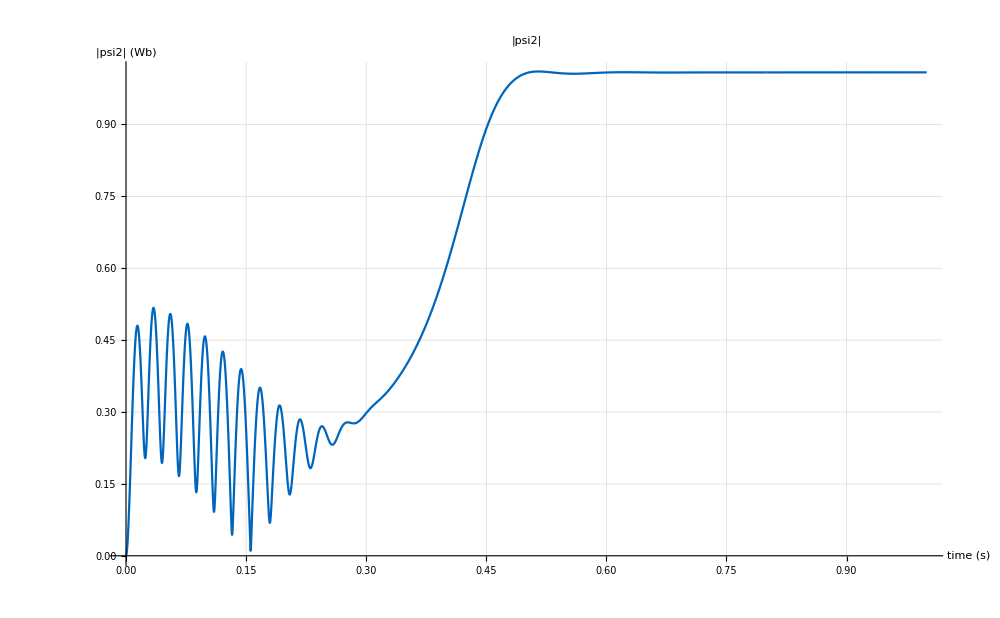

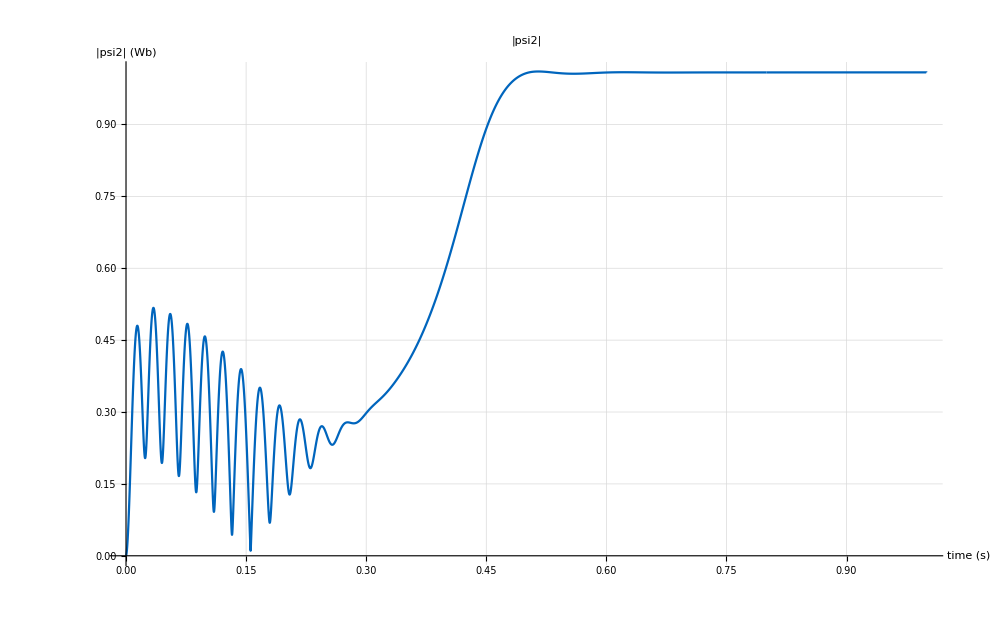

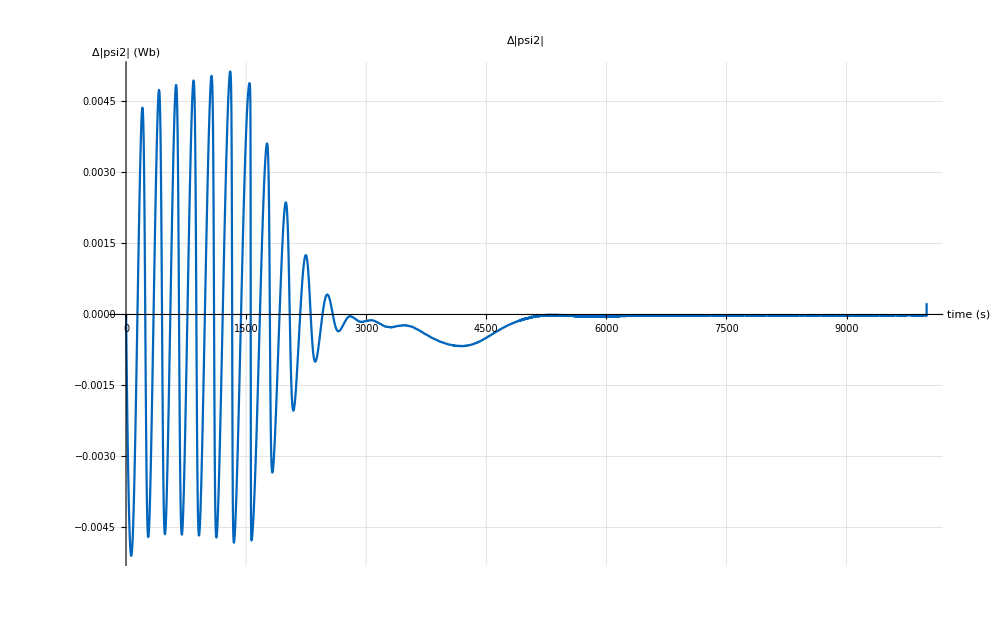

```mathematica
dataCurVel=Import["./../code/cmodel/outputCurVel.csv"];
ListPlot[dataCurVel[[All,1;;2]],Joined->True,PlotStyle->ctuBlue,LabelStyle->{FontFamily->"Times New Roman",15,Black, Bold},AxesOrigin->{0,0},GridLines->Automatic,AxesLabel->{"time (s)","|psi2| (Wb)"},PlotLabel->"|psi2|",PlotRangeClipping->False,ImageSize->1000,PlotRange->All]

dataCurVel2=Import["./../code/cmodel/outputCurVel2.csv"];
ListPlot[dataCurVel2[[All,1;;2]],Joined->True,PlotStyle->ctuBlue,LabelStyle->{FontFamily->"Times New Roman",15,Black, Bold},AxesOrigin->{0,0},GridLines->Automatic,AxesLabel->{"time (s)","|psi2| (Wb)"},PlotLabel->"|psi2|",PlotRangeClipping->False,ImageSize->1000,PlotRange->All]

ListPlot[dataCurVel[[All,2]]-dataCurVel2[[All,2]],Joined->True,PlotStyle->ctuBlue,LabelStyle->{FontFamily->"Times New Roman",15,Black, Bold},AxesOrigin->{0,0},GridLines->Automatic,AxesLabel->{"time (s)","Δ|psi2| (Wb)"},PlotLabel->"Δ|psi2|",PlotRangeClipping->False,ImageSize->1000,PlotRange->All]
```

## ASM current – velocity (I-n) model directly from ASM model values vs ASM model internal output

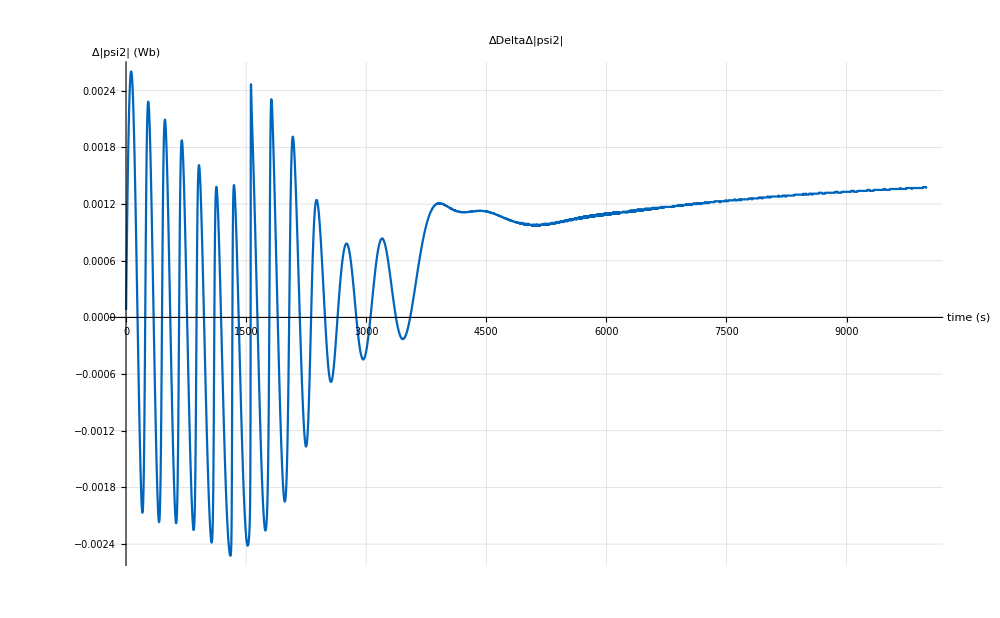

```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];

ctuBlue=RGBColor["#0065BD"];
ctuLightBlue=RGBColor["#6AADE4"];
ctuRed=RGBColor["#C60C30"];
ctuGreen=RGBColor["#A2AD00"];
ctuGreenyBlue=RGBColor["#00B2A9"];
ctuOrange=RGBColor["#E05206"];
ctuYellow=RGBColor["#F0AB00"];
dataCurVel=Import["./../code/cmodel/outputCurVel.csv"];
dataASM=Import["./../code/cmodel/outputASM.csv"];
ListPlot[dataCurVel[[2;;-1,2]]-dataASM[[2;;-1,6]],Joined->True,PlotStyle->ctuBlue,LabelStyle->{FontFamily->"Times New Roman",15,Black, Bold},AxesOrigin->{0,0},GridLines->Automatic,AxesLabel->{"time (s)","Δ|psi2| (Wb)"},PlotLabel->"ΔDeltaΔ|psi2|",PlotRangeClipping->False,ImageSize->1000,PlotRange->All]
```